```mathematica
soln = Solve[q((1-x)^4-1)+2(x^2-2x)(p^2(1-p)^2- (1-p)^4*(1-x)^2)==0,x]
```

{{x→0},{x→2},{x→(2-8 p+12 p^2-8 p^3+2 p^4-q-√(4 p^2-24 p^3+60 p^4-80 p^5+60 p^6-24 p^7+4 p^8+2 q-8 p q+10 p^2 q-4 p^3 q-q^2))/(2-8 p+12 p^2-8 p^3+2 p^4-q)},{x→(2-8 p+12 p^2-8 p^3+2 p^4-q+√(4 p^2-24 p^3+60 p^4-80 p^5+60 p^6-24 p^7+4 p^8+2 q-8 p q+10 p^2 q-4 p^3 q-q^2))/(2-8 p+12 p^2-8 p^3+2 p^4-q)}}

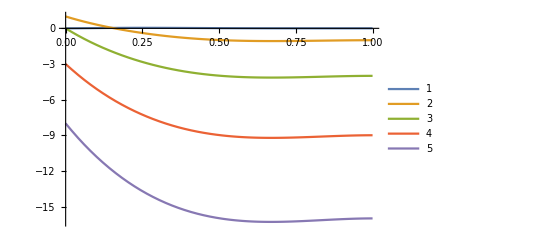

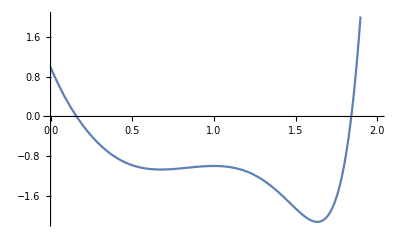

{{x→1/2 ((1-ⅈ)-√2)},{x→1/2 ((1+ⅈ)-√2)},{x→1/2 ((1-ⅈ)+√2)},{x→1/2 ((1+ⅈ)+√2)},{x→1/2 (2-2^(3/4))},{x→1/2 (2-ⅈ 2^(3/4))},{x→1/2 (2+ⅈ 2^(3/4))},{x→1/2 (2+2^(3/4))}}

```mathematica
f[p_,q_]=4 p^2-24 p^3+60 p^4-80 p^5+60 p^6-24 p^7+4 p^8+2 q-8 p q+10 p^2 q-4 p^3 q-q^2;
curves= Table[f[x,m],{m,0,4}];
Plot[curves,{x,0,1},PlotLegends->Automatic]
Plot[f[x,1],{x,0,2.001}]
Solve[f[x,1]==0,x]
```

```mathematica
f[1,1]
```

-1

```mathematica
N[1/2 (2-2^(3/4))]
```

0.159104

```mathematica
TeXForm[(2-8 p+12 p^2-8 p^3+2 p^4-q-√(4 p^2-24 p^3+60 p^4-80 p^5+60 p^6-24 p^7+4 p^8+2 q-8 p q+10 p^2 q-4 p^3 q-q^2))/(2-8 p+12 p^2-8 p^3+2 p^4-q)]
```

\frac{2 p^4-8 p^3+12 p^2-\sqrt{4 p^8-24 p^7+60 p^6-80 p^5+60 p^4-4 p^3 q-24 p^3+10 p^2
   q+4 p^2-8 p q-q^2+2 q}-8 p-q+2}{2 p^4-8 p^3+12 p^2-8 p-q+2}

```mathematica
-((-2+8 p-12 p^2+8 p^3-2 p^4+q+√(60 p^4-80 p^5+60 p^6-24 p^7+4 p^8-8 p q-(-2+q) q-4 p^3 (6+q)+2 p^2 (2+5 q)))/(2-8 p+12 p^2-8 p^3+2 p^4-q))/.p->0.1591035847462855
```

-((-1.+q+√(0.0312045-1.27283 q-(-2+q) q-0.0161102 (6+q)+0.0506279 (2+5 q)))/(1.-q))

```mathematica
(2-8 p+12 p^2-8 p^3+2 p^4-q+√(4 p^2-24 p^3+60 p^4-80 p^5+60 p^6-24 p^7+4 p^8+2 q-8 p q+10 p^2 q-4 p^3 q-q^2))/(2-8 p+12 p^2-8 p^3+2 p^4-q)/.p->0.1591035847462855
```

(1.-q+√(0.0357993+0.964201 q-q^2))/(1.-q)

```mathematica
f[0.1591035847462855,1]
```

-2.77556×10^-17

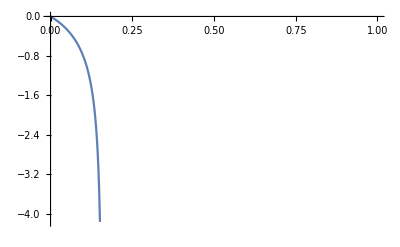

```mathematica
g[p_]:=(2-8 p+12 p^2-8 p^3+2 p^4-1-√(4 p^2-24 p^3+60 p^4-80 p^5+60 p^6-24 p^7+4 p^8+2 -8 p +10 p^2 -4 p^3 -1^2))/(2-8 p+12 p^2-8 p^3+2 p^4-1)
g2[p_]:=(2-8 p+12 p^2-8 p^3+2 p^4-2-√(4 p^2-24 p^3+60 p^4-80 p^5+60 p^6-24 p^7+4 p^8+2 *2-8 p *2+10 p^2 *2-4 p^3 *2-2^2))/(2-8 p+12 p^2-8 p^3+2 p^4-2)
Plot[{g[p],g2[p_]},{p,0,1}]
```

```mathematica
Table[g2[p*0.1],{p,Range[0,10]}]
```

{Indeterminate,1.+1.71213 ⅈ,1.+1.318 ⅈ,1.+1.17218 ⅈ,1.+1.1023 ⅈ,1.+1.06458 ⅈ,1.+1.04182 ⅈ,1.+1.02598 ⅈ,1.+1.01353 ⅈ,1.+1.00409 ⅈ,1.+1. ⅈ}

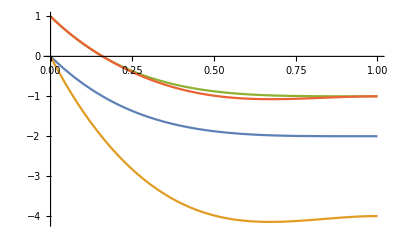

```mathematica
Plot[{(2-8 p+12 p^2-8 p^3+2 p^4-2),4 p^2-24 p^3+60 p^4-80 p^5+60 p^6-24 p^7+4 p^8+2 *2-8 p *2+10 p^2 *2-4 p^3 *2-2^2,(2-8 p+12 p^2-8 p^3+2 p^4-1),4 p^2-24 p^3+60 p^4-80 p^5+60 p^6-24 p^7+4 p^8+2 -8 p +10 p^2 -4 p^3 -1^2},{p,0,1}]
```

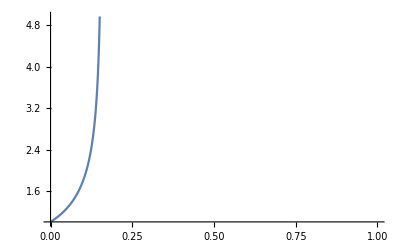

```mathematica
Plot[√(4 p^2-24 p^3+60 p^4-80 p^5+60 p^6-24 p^7+4 p^8+2 -8 p +10 p^2 -4 p^3 -1^2)/(2-8 p+12 p^2-8 p^3+2 p^4-1),{p,0,1}]
```

```mathematica
D[2-8 p+12 p^2-8 p^3+2 p^4-2,p]/D[2-8 p+12 p^2-8 p^3+2 p^4-1,p]
```

1

```mathematica
w[a_,b_,c_,q_,p_]:=((q^2 KroneckerDelta[a,0]+q KroneckerDelta[a,1])(1-p)^2+q p^2)((1-γ)^2+(KroneckerDelta[a,0]/(q^2-1) + KroneckerDelta[a,1]/(q(q^2-1) )) γ^2) ((q^2 KroneckerDelta[b,0]+q KroneckerDelta[b,1])(1-p)^2+q p^2)((1-γ)^2+(KroneckerDelta[b,0]/(q^2-1) + KroneckerDelta[b,1]/(q(q^2-1) )) γ^2) (KroneckerDelta[c,0]/(q^4-1) + KroneckerDelta[c,1]/(q^2(q^4-1) ))+
((q^2 KroneckerDelta[a,1]+q KroneckerDelta[a,0])(1-p)^2+q p^2)((1-γ)^2+(KroneckerDelta[a,1]/(q^2-1) + KroneckerDelta[a,0]/(q(q^2-1) )) γ^2) ((q^2 KroneckerDelta[b,1]+q KroneckerDelta[b,0])(1-p)^2+q p^2)((1-γ)^2+(KroneckerDelta[b,1]/(q^2-1) + KroneckerDelta[b,0]/(q(q^2-1) )) γ^2) (KroneckerDelta[c,1]/(q^4-1) + KroneckerDelta[c,0]/(q^2(q^4-1) ))
```

```mathematica
w[1,1,1,q]
```

((p^2 q+(1-p)^2 q^2)^2 ((1-γ)^2+γ^2/(-1+q^2))^2)/(-1+q^4)+(((1-p)^2 q+p^2 q)^2 ((1-γ)^2+γ^2/(q (-1+q^2)))^2)/(q^2 (-1+q^4))

```mathematica
Expand[(p^2 q+(1-p)^2 q^2)^2 ((1-γ)^2+γ^2/(-1+q^2))^2+((1-p)^2 +p^2 )^2 ((1-γ)^2+γ^2/(q (-1+q^2)))^2,q]
```

((1-p)^2+p^2)^2 (1-γ)^4+p^4 q^2 (1-γ)^4+2 (1-p)^2 p^2 q^3 (1-γ)^4+(1-p)^4 q^4 (1-γ)^4+(2 ((1-p)^2+p^2)^2 (1-γ)^2 γ^2)/(q (-1+q^2))+(2 p^4 q^2 (1-γ)^2 γ^2)/(-1+q^2)+(4 (1-p)^2 p^2 q^3 (1-γ)^2 γ^2)/(-1+q^2)+(2 (1-p)^4 q^4 (1-γ)^2 γ^2)/(-1+q^2)+(((1-p)^2+p^2)^2 γ^4)/(q^2 (-1+q^2)^2)+(p^4 q^2 γ^4)/((-1+q^2)^2)+(2 (1-p)^2 p^2 q^3 γ^4)/((-1+q^2)^2)+((1-p)^4 q^4 γ^4)/((-1+q^2)^2)

```mathematica
w[1,1,0,q]
```

((p^2 q+(1-p)^2 q^2)^2 ((1-γ)^2+γ^2/(-1+q^2))^2)/(q^2 (-1+q^4))+(((1-p)^2 q+p^2 q)^2 ((1-γ)^2+γ^2/(q (-1+q^2)))^2)/(-1+q^4)

```mathematica
Simplify[Expand[(p^2 +(1-p)^2 q)^2 ((1-γ)^2+γ^2/(-1+q^2))^2+((1-p)^2 q+p^2 q)^2 ((1-γ)^2+γ^2/(q (-1+q^2)))^2,q]]
```

p^4 (-1+γ)^4+2 (-1+p)^2 p^2 q (-1+γ)^4+2 (-1+p)^4 q^2 (-1+γ)^4+2 (-1+p)^2 p^2 q^2 (-1+γ)^4+p^4 q^2 (-1+γ)^4+(2 p^4 (-1+γ)^2 γ^2)/(-1+q^2)+(2 (-1+p)^4 q (-1+γ)^2 γ^2)/(-1+q^2)+(8 (-1+p)^2 p^2 q (-1+γ)^2 γ^2)/(-1+q^2)+(2 p^4 q (-1+γ)^2 γ^2)/(-1+q^2)+(2 (-1+p)^4 q^2 (-1+γ)^2 γ^2)/(-1+q^2)+((-1+p)^4 γ^4)/((-1+q^2)^2)+(2 (-1+p)^2 p^2 γ^4)/((-1+q^2)^2)+(2 p^4 γ^4)/((-1+q^2)^2)+(2 (-1+p)^2 p^2 q γ^4)/((-1+q^2)^2)+((-1+p)^4 q^2 γ^4)/((-1+q^2)^2)

```mathematica
allProbs={};
probFun[q_]:=p/.{ NSolve[2((1-p)^4+(1-p)^2 p^2)/(q(1-p)^4) == q((1-p)^4+(1-p)^2 p^2)/(p^2+(1-p)^2)^2 - (p^2+(1-p)^2)^2/(1-p)^4+(1-p)^2 p^2 ,p][[-1]][[1]]}
For[ i=2,i<100,i++,
AppendTo[allProbs,probFun[i]]
]
```

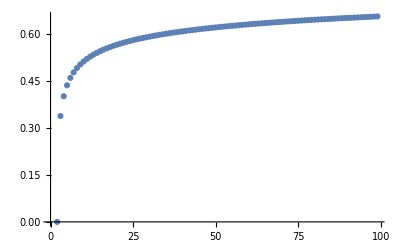

```mathematica
ListPlot[Transpose[{Range[2,99], allProbs}]]
```

```mathematica
q1=1000000000000000000000000000000000000000000;
NSolve[2((1-p)^4+(1-p)^2 p^2)/(q1(1-p)^4) == q1((1-p)^4+(1-p)^2 p^2)/(p^2+(1-p)^2)^2 - (p^2+(1-p)^2)^2/(1-p)^4+(1-p)^2 p^2 ,p,Reals]
```

{{p→1.},{p→1.}}

```mathematica
w[a_,b_,c_,q_,p_]:=((q^2 KroneckerDelta[a,0]+q KroneckerDelta[a,1])(1-p)^2+q p^2)((1-γ)^2+(KroneckerDelta[a,0]/(q^2-1) + KroneckerDelta[a,1]/(q(q^2-1) )) γ^2) ((q^2 KroneckerDelta[b,0]+q KroneckerDelta[b,1])(1-p)^2+q p^2)((1-γ)^2+(KroneckerDelta[b,0]/(q^2-1) + KroneckerDelta[b,1]/(q(q^2-1) )) γ^2) (KroneckerDelta[c,0]/(q^4-1) + KroneckerDelta[c,1]/(q^2(q^4-1) ))+
((q^2 KroneckerDelta[a,1]+q KroneckerDelta[a,0])(1-p)^2+q p^2)((1-γ)^2+(KroneckerDelta[a,1]/(q^2-1) + KroneckerDelta[a,0]/(q(q^2-1) )) γ^2) ((q^2 KroneckerDelta[b,1]+q KroneckerDelta[b,0])(1-p)^2+q p^2)((1-γ)^2+(KroneckerDelta[b,1]/(q^2-1) + KroneckerDelta[b,0]/(q(q^2-1) )) γ^2) (KroneckerDelta[c,1]/(q^4-1) + KroneckerDelta[c,0]/(q^2(q^4-1) ))
```

```mathematica
wg[c_,τ_,q_]:= KroneckerDelta[c,τ]/(q^2-1) +(1- KroneckerDelta[c,τ])/(q(q^2-1) )
wd[a_,τ_,q_,p_]:= ((q^2KroneckerDelta[a,τ]+q (1-KroneckerDelta[a,τ]))(1-p)^2+q p^2) (1-γ)^2 + wg[a,τ,q](q^2KroneckerDelta[a,0]+q KroneckerDelta[a,1])((q^2KroneckerDelta[τ,0]+q KroneckerDelta[τ,1])(1-p)^2 + q (q^2 KroneckerDelta[τ,0] + q KroneckerDelta[τ,1] )p^2) γ^2
w3[a_,b_,c_,q_,p_]:=wd[a,0,q,p] wd[b,0,q,p]wg[c,0,q^2]+wd[a,1,q,p] wd[b,1,q,p]wg[c,1,q^2]
```

```mathematica
w3[1,1,1,q,p]
```

(((p^2 q+(1-p)^2 q^2) (1-γ)^2+(q ((1-p)^2 q+p^2 q^2) γ^2)/(-1+q^2))^2)/(-1+q^4)+((((1-p)^2 q+p^2 q) (1-γ)^2+(((1-p)^2 q^2+p^2 q^3) γ^2)/(-1+q^2))^2)/(q^2 (-1+q^4))

```mathematica
Expand[((p^2 q+(1-p)^2 q^2) (1-γ)^2+(q ((1-p)^2 q+p^2 q^2) γ^2)/(-1+q^2))^2+(((1-p)^2 +p^2 ) (1-γ)^2+(((1-p)^2 q+p^2 q^2) γ^2)/(-1+q^2))^2,q]
```

((1-p)^2+p^2)^2 (1-γ)^4+p^4 q^2 (1-γ)^4+2 (1-p)^2 p^2 q^3 (1-γ)^4+(1-p)^4 q^4 (1-γ)^4+(2 (1-p)^2 ((1-p)^2+p^2) q (1-γ)^2 γ^2)/(-1+q^2)+(2 p^2 ((1-p)^2+p^2) q^2 (1-γ)^2 γ^2)/(-1+q^2)+(2 (1-p)^2 p^2 q^3 (1-γ)^2 γ^2)/(-1+q^2)+(2 (1-p)^4 q^4 (1-γ)^2 γ^2)/(-1+q^2)+(2 p^4 q^4 (1-γ)^2 γ^2)/(-1+q^2)+(2 (1-p)^2 p^2 q^5 (1-γ)^2 γ^2)/(-1+q^2)+((1-p)^4 q^2 γ^4)/((-1+q^2)^2)+(2 (1-p)^2 p^2 q^3 γ^4)/((-1+q^2)^2)+((1-p)^4 q^4 γ^4)/((-1+q^2)^2)+(p^4 q^4 γ^4)/((-1+q^2)^2)+(2 (1-p)^2 p^2 q^5 γ^4)/((-1+q^2)^2)+(p^4 q^6 γ^4)/((-1+q^2)^2)

```mathematica
w3[0,0,0,q,p]
```

((((1-p)^2 q+p^2 q) (1-γ)^2+(q ((1-p)^2 q+p^2 q^2) γ^2)/(-1+q^2))^2)/(q^2 (-1+q^4))+(((p^2 q+(1-p)^2 q^2) (1-γ)^2+(q^2 ((1-p)^2 q^2+p^2 q^3) γ^2)/(-1+q^2))^2)/(-1+q^4)

```mathematica
Expand[(((1-p)^2 +p^2 ) (1-γ)^2+(((1-p)^2 q+p^2 q^2) γ^2)/(-1+q^2))^2+((p^2 q+(1-p)^2 q^2) (1-γ)^2+(q^2 ((1-p)^2 q^2+p^2 q^3) γ^2)/(-1+q^2))^2,q]
```

((1-p)^2+p^2)^2 (1-γ)^4+p^4 q^2 (1-γ)^4+2 (1-p)^2 p^2 q^3 (1-γ)^4+(1-p)^4 q^4 (1-γ)^4+(2 (1-p)^2 ((1-p)^2+p^2) q (1-γ)^2 γ^2)/(-1+q^2)+(2 p^2 ((1-p)^2+p^2) q^2 (1-γ)^2 γ^2)/(-1+q^2)+(2 (1-p)^2 p^2 q^5 (1-γ)^2 γ^2)/(-1+q^2)+(2 (1-p)^4 q^6 (1-γ)^2 γ^2)/(-1+q^2)+(2 p^4 q^6 (1-γ)^2 γ^2)/(-1+q^2)+(2 (1-p)^2 p^2 q^7 (1-γ)^2 γ^2)/(-1+q^2)+((1-p)^4 q^2 γ^4)/((-1+q^2)^2)+(2 (1-p)^2 p^2 q^3 γ^4)/((-1+q^2)^2)+(p^4 q^4 γ^4)/((-1+q^2)^2)+((1-p)^4 q^8 γ^4)/((-1+q^2)^2)+(2 (1-p)^2 p^2 q^9 γ^4)/((-1+q^2)^2)+(p^4 q^10 γ^4)/((-1+q^2)^2)

```mathematica
Clear[q,p]
Expand[Simplify[w3[0,0,1,q,p]]*(-1+q^4),q]
```

-w3[0,0,1,q,p]+q^4 w3[0,0,1,q,p]

```mathematica
w3[0,1,0,q,p]
```

((((1-p)^2 q+p^2 q) (1-γ)^2+(q ((1-p)^2 q+p^2 q^2) γ^2)/(-1+q^2)) ((p^2 q+(1-p)^2 q^2) (1-γ)^2+(q ((1-p)^2 q+p^2 q^2) γ^2)/(-1+q^2)))/(q^2 (-1+q^4))+((((1-p)^2 q+p^2 q) (1-γ)^2+(((1-p)^2 q^2+p^2 q^3) γ^2)/(-1+q^2)) ((p^2 q+(1-p)^2 q^2) (1-γ)^2+(q^2 ((1-p)^2 q^2+p^2 q^3) γ^2)/(-1+q^2)))/(-1+q^4)

```mathematica
Expand[(((1-p)^2 +p^2 ) (1-γ)^2+(((1-p)^2 q+p^2 q^2) γ^2)/(-1+q^2)) ((p^2 +(1-p)^2 q) (1-γ)^2+(((1-p)^2 q+p^2 q^2) γ^2)/(-1+q^2))+(((1-p)^2 q+p^2 q) (1-γ)^2+(((1-p)^2 q^2+p^2 q^3) γ^2)/(-1+q^2)) ((p^2 q+(1-p)^2 q^2) (1-γ)^2+(q^2 ((1-p)^2 q^2+p^2 q^3) γ^2)/(-1+q^2)),q]
```

p^2 ((1-p)^2+p^2) (1-γ)^4+(1-p)^2 ((1-p)^2+p^2) q (1-γ)^4+(1-p)^2 p^2 q^2 (1-γ)^4+p^4 q^2 (1-γ)^4+(1-p)^4 q^3 (1-γ)^4+(1-p)^2 p^2 q^3 (1-γ)^4+((1-p)^2 p^2 q (1-γ)^2 γ^2)/(-1+q^2)+((1-p)^2 ((1-p)^2+p^2) q (1-γ)^2 γ^2)/(-1+q^2)+((1-p)^4 q^2 (1-γ)^2 γ^2)/(-1+q^2)+(p^4 q^2 (1-γ)^2 γ^2)/(-1+q^2)+(p^2 ((1-p)^2+p^2) q^2 (1-γ)^2 γ^2)/(-1+q^2)+(2 (1-p)^2 p^2 q^3 (1-γ)^2 γ^2)/(-1+q^2)+((1-p)^4 q^4 (1-γ)^2 γ^2)/(-1+q^2)+(p^4 q^4 (1-γ)^2 γ^2)/(-1+q^2)+((1-p)^4 q^5 (1-γ)^2 γ^2)/(-1+q^2)+(2 (1-p)^2 p^2 q^5 (1-γ)^2 γ^2)/(-1+q^2)+((1-p)^2 p^2 q^6 (1-γ)^2 γ^2)/(-1+q^2)+(p^4 q^6 (1-γ)^2 γ^2)/(-1+q^2)+((1-p)^4 q^2 γ^4)/((-1+q^2)^2)+(2 (1-p)^2 p^2 q^3 γ^4)/((-1+q^2)^2)+(p^4 q^4 γ^4)/((-1+q^2)^2)+((1-p)^4 q^6 γ^4)/((-1+q^2)^2)+(2 (1-p)^2 p^2 q^7 γ^4)/((-1+q^2)^2)+(p^4 q^8 γ^4)/((-1+q^2)^2)

```mathematica
w3[0,0,1,q,p]
```

((((1-p)^2 q+p^2 q) (1-γ)^2+(q ((1-p)^2 q+p^2 q^2) γ^2)/(-1+q^2))^2)/(-1+q^4)+(((p^2 q+(1-p)^2 q^2) (1-γ)^2+(q^2 ((1-p)^2 q^2+p^2 q^3) γ^2)/(-1+q^2))^2)/(q^2 (-1+q^4))

```mathematica
Expand[(((1-p)^2 q+p^2 q) (1-γ)^2+(q ((1-p)^2 q+p^2 q^2) γ^2)/(-1+q^2))^2+((p^2 +(1-p)^2 q) (1-γ)^2+(q ((1-p)^2 q^2+p^2 q^3) γ^2)/(-1+q^2))^2,q]
```

p^4 (1-γ)^4+2 (1-p)^2 p^2 q (1-γ)^4+2 (1-p)^4 q^2 (1-γ)^4+2 (1-p)^2 p^2 q^2 (1-γ)^4+p^4 q^2 (1-γ)^4+(2 (1-p)^4 q^3 (1-γ)^2 γ^2)/(-1+q^2)+(4 (1-p)^2 p^2 q^3 (1-γ)^2 γ^2)/(-1+q^2)+(2 (1-p)^4 q^4 (1-γ)^2 γ^2)/(-1+q^2)+(2 (1-p)^2 p^2 q^4 (1-γ)^2 γ^2)/(-1+q^2)+(4 p^4 q^4 (1-γ)^2 γ^2)/(-1+q^2)+(2 (1-p)^2 p^2 q^5 (1-γ)^2 γ^2)/(-1+q^2)+((1-p)^4 q^4 γ^4)/((-1+q^2)^2)+(2 (1-p)^2 p^2 q^5 γ^4)/((-1+q^2)^2)+((1-p)^4 q^6 γ^4)/((-1+q^2)^2)+(p^4 q^6 γ^4)/((-1+q^2)^2)+(2 (1-p)^2 p^2 q^7 γ^4)/((-1+q^2)^2)+(p^4 q^8 γ^4)/((-1+q^2)^2)

```mathematica
w3[1,0,1,q,p]
```

((((1-p)^2 q+p^2 q) (1-γ)^2+(q ((1-p)^2 q+p^2 q^2) γ^2)/(-1+q^2)) ((p^2 q+(1-p)^2 q^2) (1-γ)^2+(q ((1-p)^2 q+p^2 q^2) γ^2)/(-1+q^2)))/(-1+q^4)+((((1-p)^2 q+p^2 q) (1-γ)^2+(((1-p)^2 q^2+p^2 q^3) γ^2)/(-1+q^2)) ((p^2 q+(1-p)^2 q^2) (1-γ)^2+(q^2 ((1-p)^2 q^2+p^2 q^3) γ^2)/(-1+q^2)))/(q^2 (-1+q^4))

```mathematica
Expand[(((1-p)^2 q+p^2 q) (1-γ)^2+(q ((1-p)^2 q+p^2 q^2) γ^2)/(-1+q^2)) ((p^2 q+(1-p)^2 q^2) (1-γ)^2+(q ((1-p)^2 q+p^2 q^2) γ^2)/(-1+q^2))+(((1-p)^2 +p^2 ) (1-γ)^2+(((1-p)^2 q+p^2 q^2) γ^2)/(-1+q^2)) ((p^2 +(1-p)^2 q) (1-γ)^2+(q ((1-p)^2 q^2+p^2 q^3) γ^2)/(-1+q^2)),q]
```

p^2 ((1-p)^2+p^2) (1-γ)^4+(1-p)^2 ((1-p)^2+p^2) q (1-γ)^4+(1-p)^2 p^2 q^2 (1-γ)^4+p^4 q^2 (1-γ)^4+(1-p)^4 q^3 (1-γ)^4+(1-p)^2 p^2 q^3 (1-γ)^4+((1-p)^2 p^2 q (1-γ)^2 γ^2)/(-1+q^2)+((1-p)^4 q^2 (1-γ)^2 γ^2)/(-1+q^2)+(p^4 q^2 (1-γ)^2 γ^2)/(-1+q^2)+((1-p)^4 q^3 (1-γ)^2 γ^2)/(-1+q^2)+(3 (1-p)^2 p^2 q^3 (1-γ)^2 γ^2)/(-1+q^2)+((1-p)^2 ((1-p)^2+p^2) q^3 (1-γ)^2 γ^2)/(-1+q^2)+((1-p)^4 q^4 (1-γ)^2 γ^2)/(-1+q^2)+((1-p)^2 p^2 q^4 (1-γ)^2 γ^2)/(-1+q^2)+(2 p^4 q^4 (1-γ)^2 γ^2)/(-1+q^2)+(p^2 ((1-p)^2+p^2) q^4 (1-γ)^2 γ^2)/(-1+q^2)+((1-p)^2 p^2 q^5 (1-γ)^2 γ^2)/(-1+q^2)+(2 (1-p)^4 q^4 γ^4)/((-1+q^2)^2)+(4 (1-p)^2 p^2 q^5 γ^4)/((-1+q^2)^2)+(2 p^4 q^6 γ^4)/((-1+q^2)^2)

```mathematica
w3[0,1,0,q,p]
```

((((1-p)^2 q+p^2 q) (1-γ)^2+(q ((1-p)^2 q+p^2 q^2) γ^2)/(-1+q^2)) ((p^2 q+(1-p)^2 q^2) (1-γ)^2+(q ((1-p)^2 q+p^2 q^2) γ^2)/(-1+q^2)))/(q^2 (-1+q^4))+((((1-p)^2 q+p^2 q) (1-γ)^2+(((1-p)^2 q^2+p^2 q^3) γ^2)/(-1+q^2)) ((p^2 q+(1-p)^2 q^2) (1-γ)^2+(q^2 ((1-p)^2 q^2+p^2 q^3) γ^2)/(-1+q^2)))/(-1+q^4)

```mathematica
Expand[(((1-p)^2 +p^2 ) (1-γ)^2+(((1-p)^2 q+p^2 q^2) γ^2)/(-1+q^2)) ((p^2 +(1-p)^2 q) (1-γ)^2+(((1-p)^2 q+p^2 q^2) γ^2)/(-1+q^2))+(((1-p)^2 q+p^2 q) (1-γ)^2+(((1-p)^2 q^2+p^2 q^3) γ^2)/(-1+q^2)) ((p^2 q+(1-p)^2 q^2) (1-γ)^2+(q^2 ((1-p)^2 q^2+p^2 q^3) γ^2)/(-1+q^2)),q]
```

p^2 ((1-p)^2+p^2) (1-γ)^4+(1-p)^2 ((1-p)^2+p^2) q (1-γ)^4+(1-p)^2 p^2 q^2 (1-γ)^4+p^4 q^2 (1-γ)^4+(1-p)^4 q^3 (1-γ)^4+(1-p)^2 p^2 q^3 (1-γ)^4+((1-p)^2 p^2 q (1-γ)^2 γ^2)/(-1+q^2)+((1-p)^2 ((1-p)^2+p^2) q (1-γ)^2 γ^2)/(-1+q^2)+((1-p)^4 q^2 (1-γ)^2 γ^2)/(-1+q^2)+(p^4 q^2 (1-γ)^2 γ^2)/(-1+q^2)+(p^2 ((1-p)^2+p^2) q^2 (1-γ)^2 γ^2)/(-1+q^2)+(2 (1-p)^2 p^2 q^3 (1-γ)^2 γ^2)/(-1+q^2)+((1-p)^4 q^4 (1-γ)^2 γ^2)/(-1+q^2)+(p^4 q^4 (1-γ)^2 γ^2)/(-1+q^2)+((1-p)^4 q^5 (1-γ)^2 γ^2)/(-1+q^2)+(2 (1-p)^2 p^2 q^5 (1-γ)^2 γ^2)/(-1+q^2)+((1-p)^2 p^2 q^6 (1-γ)^2 γ^2)/(-1+q^2)+(p^4 q^6 (1-γ)^2 γ^2)/(-1+q^2)+((1-p)^4 q^2 γ^4)/((-1+q^2)^2)+(2 (1-p)^2 p^2 q^3 γ^4)/((-1+q^2)^2)+(p^4 q^4 γ^4)/((-1+q^2)^2)+((1-p)^4 q^6 γ^4)/((-1+q^2)^2)+(2 (1-p)^2 p^2 q^7 γ^4)/((-1+q^2)^2)+(p^4 q^8 γ^4)/((-1+q^2)^2)

```mathematica
Simplify[w3[0,1,0,q,p]-w3[1,0,1,q,p]]
Simplify[-(-1+γ)^2+q^2 (-1+γ)^2+q γ^2-2 p (-(-1+γ)^2+q^2 (-1+γ)^2+q γ^2)+p^2 (1+q) (-2 (-1+γ)^2+q (2-4 γ+3 γ^2))]
```

1/(-1+q^4)q (1-2 p+p^2 (1+q)) γ^2 (-(-1+γ)^2+q^2 (-1+γ)^2+q γ^2-2 p (-(-1+γ)^2+q^2 (-1+γ)^2+q γ^2)+p^2 (1+q) (-2 (-1+γ)^2+q (2-4 γ+3 γ^2)))

-(-1+γ)^2+q^2 (-1+γ)^2+q γ^2-2 p (-(-1+γ)^2+q^2 (-1+γ)^2+q γ^2)+p^2 (1+q) (-2 (-1+γ)^2+q (2-4 γ+3 γ^2))

```mathematica
-(-1+γ)^2+q^2 (-1+γ)^2+q γ^2-2 p (-(-1+γ)^2+q^2 (-1+γ)^2+q γ^2)+p^2 (1+q) (-2 (-1+γ)^2+q (2-4 γ+3 γ^2))
```

```mathematica
t1[q_,p_]:=Tanh[1/2 Log[(p^2+(1-p)^2)^2]/(q (1-p)^4 + (1-p)^2 p^2)]
t2[q_,p_]:=Tanh[1/2 Log[(q (1-p)^4 + (1-p)^2 p^2) /(q(1-p)^4)]]
q2=2;
NSolve[1+t1[q2,p1]^2t2[q2,p1]+t1[q2,p1]^2+2 t1[q2,p1]t2[q2,p1]- 2t1[q2,p1]-t2[q2,p1]==0,p1,Reals]
```

$Aborted

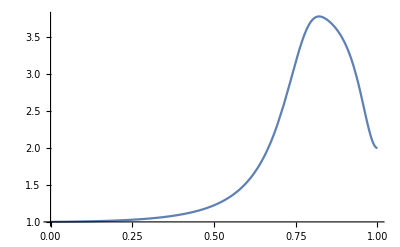

```mathematica
q2=100;
Plot[1+t1[q2,p1]^2t2[q2,p1]+t1[q2,p1]^2+2 t1[q2,p1]t2[q2,p1]- 2t1[q2,p1]-t2[q2,p1],{p1,0,1}]
```

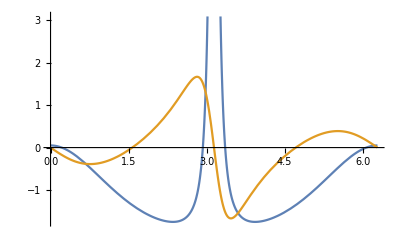

```mathematica
Plot[{(Cos[x]^2-3*Sin[x]^2-Exp[-2*e])/(1+Sin[x]^2+2 Exp[-e] Cos[x]+Exp[-2*e])/.{e->0.1},-2*Sin[x]*Cos[x]/(1+Sin[x]^2+2 Exp[-e] Cos[x]+Exp[-2*e])/.{e->0.6}},{x,0,2*Pi}]
```

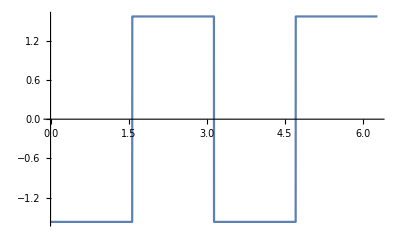

```mathematica
Plot[Arg[(Cos[x]^2-3*Sin[x]^2-Exp[-2*e])/(1+Sin[x]^2+2 Exp[-e] Cos[x]+Exp[-2*e])I*2*Sin[x]*Cos[x]/(1+Sin[x]^2+2 Exp[-e] Cos[x]+Exp[-2*e])/.{e->-0.4}],{x,0,2*Pi}]
```

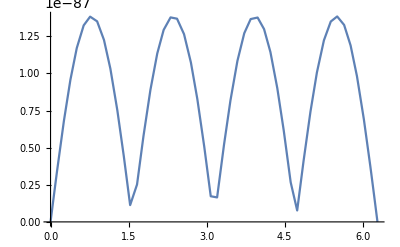

```mathematica
Plot[Abs[(Cos[x]^2-3*Sin[x]^2-Exp[-2*e])/(1+Sin[x]^2+2 Exp[-e] Cos[x]+Exp[-2*e])I*2*Sin[x]*Cos[x]/(1+Sin[x]^2+2 Exp[-e] Cos[x]+Exp[-2*e])/.{e->-100}],{x,0,2*Pi}]
```

```mathematica
D[2*Cosh[2Pi x/b]/((Sinh[2Pi x/b])^5),x]
```

-(16 π Coth[(2 π x)/b]^2 Csch[(2 π x)/b]^4)/b-(4 π Csch[(2 π x)/b]^6)/b

```mathematica
D[4 Pi^2/b^2/(Sinh[2Pi x/b])^2,x]*2 Pi/b/Sinh[2Pi x/b]/2
```

-(16 π^4 Coth[(2 π x)/b] Csch[(2 π x)/b]^3)/b^4

```mathematica
D[4 Pi^2/b^2/(Sinh[2Pi x/b])^2,x]*4 Pi^2/b^2/(Sinh[2Pi x/b])^2/2
```

-(32 π^5 Coth[(2 π x)/b] Csch[(2 π x)/b]^4)/b^5

```mathematica
D[-D[4 Pi^2/b^2/(Sinh[2Pi x/b])^2,x]*4 Pi^2/b^2/(Sinh[2Pi x/b])^2/2,x]
```

-(256 π^6 Coth[(2 π x)/b]^2 Csch[(2 π x)/b]^4)/b^6-(64 π^6 Csch[(2 π x)/b]^6)/b^6

```mathematica
Simplify[-(256 π^6 Coth[(2 π x)/b]^2 Csch[(2 π x)/b]^4)/b^6-(64 π^6 Csch[(2 π x)/b]^6)/b^6]*4 Pi^2/b^2/(Sinh[2Pi x/b])^2
```

-(256 π^8 (3+2 Cosh[(4 π x)/b]) Csch[(2 π x)/b]^8)/b^8

```mathematica
Integrate[-(256 π^8 (3+2 Cosh[(4 π x)/b]) Csch[(2 π x)/b]^8)/b^8,{x,-Infinity,-2}]
```

$Aborted

```mathematica
Integrate[-256 π^8 (3+2 Cosh[4 π x]) Csch[2 π x]^8,{x,-Infinity,-0}]
```

∫_(-∞)^0 -256 π^8 (3+2 Cosh[4 π x]) Csch[2 π x]^8ⅆx

```mathematica
-(32 π^5 Coth[(2 π x)/b] Csch[(2 π x)/b]^4)/b^5/.{x->0}
```

ComplexInfinity